This notebook is to study the effect of \CapitalTheta (A) on the length distribution for kinetic+rotation+vibration energy.

```mathematica
J=1
gamma = 1.5
vibration = 1
Timing[Jkrj=Table[u/.FindRoot[A×x^-3×ⅇ^(-J×x)×(ⅇ^-u+gamma×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-u×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))-1,{u,-3},MaxIterations->10000],{A,{1,10,100,1000,10000}},{x,0.01,15,0.1}]]
```

1

1.5

1

General::munfl: 175.883/(2039298274118911624692976044998614874707514564867423598278106834085399394«166»2875200268932124981878786621440000000000000000000000000000000000000000000) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (176.876 89)/(3140720980624160378682208931648383624025948004369661929299574944043649354«170»5196699124005923162587377172480000000000000000000000000000000000000000000) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (177.87 32041)/(1967912952039486410074698472392244211142178500577942771660527668438869812«175»4773711963133521399878873251840000000000000000000000000000000000000000000) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{11636.8,{{13.8055,6.52872,4.5867,3.52726,2.87142,2.425,2.095,1.83533,1.62162,1.43994,1.28175,1.14151,1.01543,0.900819,0.795691,0.698549,0.608233,0.523823,0.44458,0.369899,0.299279,0.2323,0.168604,0.107887,0.0498844,-0.00563177,-0.0588627,-0.109985,-0.159156,-0.206516,-0.252189,-0.296288,-0.338915,-0.380161,-0.420111,-0.458841,-0.496421,-0.532915,-0.568382,-0.602876,-0.636448,-0.669144,-0.701007,-0.732078,-0.762394,-0.791989,-0.820896,-0.849146,-0.876767,-0.903785,-0.930227,-0.956114,-0.98147,-1.00632,-1.03067,-1.05455,-1.07798,-1.10097,-1.12354,-1.1457,-1.16747,-1.18885,-1.20988,-1.23054,-1.25086,-1.27086,-1.29052,-1.30988,-1.32894,-1.3477,-1.36618,-1.38438,-1.40231,-1.41999,-1.43741,-1.45458,-1.47152,-1.48822,-1.5047,-1.52095,-1.53699,-1.55282,-1.56845,-1.58387,-1.5991,-1.61415,-1.629,-1.64368,-1.65818,-1.67251,-1.68667,-1.70066,-1.7145,-1.72817,-1.7417,-1.75507,-1.76829,-1.78137,-1.79431,-1.80711,-1.81978,-1.83231,-1.84471,-1.85699,-1.86914,-1.88116,-1.89307,-1.90486,-1.91653,-1.92809,-1.93954,-1.95088,-1.96211,-1.97324,-1.98426,-1.99518,-2.00601,-2.01673,-2.02735,-2.03789,-2.04833,-2.05867,-2.06893,-2.0791,-2.08918,-2.09917,-2.10909,-2.11891,-2.12866,-2.13833,-2.14791,-2.15742,-2.16686,-2.17621,-2.1855,-2.19471,-2.20384,-2.21291,-2.22191,-2.23083,-2.23969,-2.24849,-2.25721,-2.26587,-2.27447,-2.28301,-2.29148,-2.29989,-2.30824,-2.31653},{16.1081,8.81612,6.78715,5.54843,4.66697,4.00211,3.4866,3.07872,2.74912,2.47673,2.2466,2.04825,1.8743,1.7195,1.58002,1.45306,1.33649,1.22867,1.12835,1.0345,0.946302,0.863096,0.784326,0.709529,0.638316,0.570352,0.50535,0.443059,0.383264,0.325772,0.270413,0.217036,0.165508,0.115706,0.067522,0.0208561,-0.0243813,-0.0682722,-0.110892,-0.152309,-0.192587,-0.231785,-0.269957,-0.307152,-0.343417,-0.378795,-0.413328,-0.447052,-0.480003,-0.512213,-0.543714,-0.574535,-0.604703,-0.634243,-0.663181,-0.691538,-0.719337,-0.746598,-0.77334,-0.799582,-0.825341,-0.850633,-0.875475,-0.899881,-0.923865,-0.947441,-0.970622,-0.99342,-1.01585,-1.03791,-1.05963,-1.08101,-1.10206,-1.12279,-1.14321,-1.16333,-1.18315,-1.20269,-1.22195,-1.24093,-1.25966,-1.27812,-1.29634,-1.31431,-1.33205,-1.34955,-1.36682,-1.38388,-1.40071,-1.41734,-1.43376,-1.44998,-1.466,-1.48183,-1.49747,-1.51292,-1.5282,-1.5433,-1.55823,-1.57299,-1.58758,-1.60201,-1.61628,-1.6304,-1.64437,-1.65818,-1.67185,-1.68538,-1.69876,-1.71201,-1.72512,-1.7381,-1.75094,-1.76366,-1.77626,-1.78873,-1.80108,-1.81331,-1.82542,-1.83742,-1.84931,-1.86108,-1.87275,-1.88431,-1.89576,-1.90711,-1.91836,-1.92951,-1.94056,-1.95151,-1.96237,-1.97313,-1.9838,-1.99438,-2.00487,-2.01528,-2.02559,-2.03582,-2.04597,-2.05603,-2.06602,-2.07592,-2.08574,-2.09549,-2.10515,-2.11475,-2.12426,-2.13371,-2.14308,-2.15238},{18.4107,11.1172,9.07839,7.8131,6.88075,6.13727,5.518,4.98887,4.52996,4.12863,3.77604,3.46541,3.19105,2.94791,2.73148,2.53777,2.36332,2.20518,2.06087,1.92836,1.80595,1.69226,1.58613,1.48661,1.39291,1.30437,1.22043,1.14061,1.06451,0.991776,0.922119,0.855274,0.791013,0.729137,0.669467,0.611849,0.556141,0.502219,0.44997,0.399293,0.350095,0.302292,0.255808,0.210573,0.166524,0.123599,0.0817463,0.0409138,0.00105509,-0.0378734,-0.0759123,-0.113099,-0.14947,-0.185057,-0.219892,-0.254004,-0.287421,-0.320168,-0.352269,-0.383749,-0.414629,-0.444929,-0.47467,-0.503869,-0.532545,-0.560715,-0.588394,-0.615598,-0.642341,-0.668638,-0.694501,-0.719944,-0.744978,-0.769616,-0.793868,-0.817746,-0.841258,-0.864416,-0.887229,-0.909706,-0.931855,-0.953686,-0.975206,-0.996422,-1.01734,-1.03798,-1.05833,-1.07841,-1.09822,-1.11776,-1.13706,-1.1561,-1.1749,-1.19346,-1.21179,-1.22988,-1.24776,-1.26542,-1.28286,-1.3001,-1.31713,-1.33396,-1.3506,-1.36704,-1.3833,-1.39937,-1.41526,-1.43097,-1.44651,-1.46188,-1.47708,-1.49212,-1.50699,-1.52171,-1.53628,-1.55069,-1.56496,-1.57907,-1.59305,-1.60688,-1.62058,-1.63414,-1.64756,-1.66085,-1.67402,-1.68706,-1.69997,-1.71276,-1.72543,-1.73798,-1.75041,-1.76273,-1.77494,-1.78704,-1.79902,-1.8109,-1.82268,-1.83435,-1.84592,-1.85738,-1.86875,-1.88002,-1.89119,-1.90227,-1.91326,-1.92415,-1.93495,-1.94567,-1.95629,-1.96683},{20.7133,13.4196,11.3798,10.1117,9.17364,8.42003,7.78476,7.2322,6.74102,6.29758,5.89268,5.5199,5.17471,4.85382,4.55483,4.27596,4.01586,3.77345,3.54777,3.33793,3.14303,2.9621,2.79415,2.63815,2.49306,2.35789,2.23167,2.1135,2.00258,1.89816,1.79958,1.70627,1.61769,1.53341,1.45301,1.37614,1.3025,1.23181,1.16383,1.09835,1.03517,0.974133,0.915081,0.857882,0.802414,0.748569,0.696249,0.645364,0.595834,0.547586,0.500551,0.454669,0.409883,0.366141,0.323395,0.2816,0.240717,0.200705,0.161531,0.123159,0.085561,0.0487059,0.012567,-0.0228814,-0.0576635,-0.091802,-0.125319,-0.158234,-0.190566,-0.222335,-0.253558,-0.28425,-0.314429,-0.344108,-0.373303,-0.402026,-0.430292,-0.458113,-0.4855,-0.512466,-0.539022,-0.565178,-0.590944,-0.61633,-0.641347,-0.666002,-0.690305,-0.714264,-0.737888,-0.761184,-0.784161,-0.806825,-0.829183,-0.851243,-0.873011,-0.894494,-0.915698,-0.93663,-0.957294,-0.977696,-0.997844,-1.01774,-1.03739,-1.0568,-1.07598,-1.09493,-1.11365,-1.13215,-1.15043,-1.1685,-1.18636,-1.20402,-1.22147,-1.23873,-1.2558,-1.27268,-1.28937,-1.30588,-1.32221,-1.33837,-1.35435,-1.37017,-1.38582,-1.4013,-1.41662,-1.43179,-1.4468,-1.46166,-1.47637,-1.49094,-1.50536,-1.51963,-1.53377,-1.54777,-1.56163,-1.57537,-1.58897,-1.60244,-1.61579,-1.62901,-1.64211,-1.65509,-1.66795,-1.68069,-1.69332,-1.70584,-1.71824,-1.73054,-1.74272,-1.7548},{23.0159,15.7222,13.6823,12.4139,11.4752,10.7206,10.0836,9.52851,9.03362,8.58498,8.17301,7.79088,7.43354,7.0972,6.77893,6.47646,6.18797,5.91205,5.64757,5.39365,5.1496,4.9149,4.68916,4.47213,4.26363,4.06354,3.87182,3.68842,3.5133,3.3464,3.18763,3.03683,2.89377,2.7582,2.62978,2.50814,2.3929,2.28364,2.17994,2.0814,1.98763,1.89825,1.81292,1.73132,1.65314,1.57812,1.50601,1.43659,1.36966,1.30503,1.24254,1.18203,1.12339,1.06648,1.01119,0.95742,0.905087,0.854104,0.804397,0.755897,0.708541,0.662272,0.617037,0.572788,0.529481,0.487073,0.445528,0.404809,0.364884,0.325722,0.287295,0.249576,0.212541,0.176164,0.140426,0.105304,0.0707802,0.036835,0.00345123,-0.0293877,-0.0616976,-0.0934933,-0.124789,-0.155599,-0.185935,-0.21581,-0.245237,-0.274226,-0.302788,-0.330933,-0.358673,-0.386016,-0.412973,-0.439551,-0.46576,-0.491607,-0.517102,-0.542252,-0.567064,-0.591546,-0.615705,-0.639548,-0.663082,-0.686312,-0.709246,-0.731889,-0.754247,-0.776326,-0.798132,-0.819669,-0.840945,-0.861962,-0.882727,-0.903245,-0.923519,-0.943555,-0.963358,-0.982931,-1.00228,-1.02141,-1.04032,-1.05901,-1.0775,-1.09578,-1.11386,-1.13175,-1.14944,-1.16693,-1.18424,-1.20137,-1.21831,-1.23508,-1.25167,-1.26809,-1.28434,-1.30042,-1.31634,-1.3321,-1.3477,-1.36314,-1.37844,-1.39358,-1.40857,-1.42342,-1.43812,-1.45269,-1.46711,-1.4814,-1.49555,-1.50957}}}

```mathematica
x= Range[0.01,15,0.1]
```

{0.01,0.11,0.21,0.31,0.41,0.51,0.61,0.71,0.81,0.91,1.01,1.11,1.21,1.31,1.41,1.51,1.61,1.71,1.81,1.91,2.01,2.11,2.21,2.31,2.41,2.51,2.61,2.71,2.81,2.91,3.01,3.11,3.21,3.31,3.41,3.51,3.61,3.71,3.81,3.91,4.01,4.11,4.21,4.31,4.41,4.51,4.61,4.71,4.81,4.91,5.01,5.11,5.21,5.31,5.41,5.51,5.61,5.71,5.81,5.91,6.01,6.11,6.21,6.31,6.41,6.51,6.61,6.71,6.81,6.91,7.01,7.11,7.21,7.31,7.41,7.51,7.61,7.71,7.81,7.91,8.01,8.11,8.21,8.31,8.41,8.51,8.61,8.71,8.81,8.91,9.01,9.11,9.21,9.31,9.41,9.51,9.61,9.71,9.81,9.91,10.01,10.11,10.21,10.31,10.41,10.51,10.61,10.71,10.81,10.91,11.01,11.11,11.21,11.31,11.41,11.51,11.61,11.71,11.81,11.91,12.01,12.11,12.21,12.31,12.41,12.51,12.61,12.71,12.81,12.91,13.01,13.11,13.21,13.31,13.41,13.51,13.61,13.71,13.81,13.91,14.01,14.11,14.21,14.31,14.41,14.51,14.61,14.71,14.81,14.91}

```mathematica
J05 = Jkrj[[1]]
J1 = Jkrj[[2]]
J105 = Jkrj[[3]]
J2 = Jkrj[[4]]
J205=Jkrj[[5]]
```

{13.8055,6.52872,4.5867,3.52726,2.87142,2.425,2.095,1.83533,1.62162,1.43994,1.28175,1.14151,1.01543,0.900819,0.795691,0.698549,0.608233,0.523823,0.44458,0.369899,0.299279,0.2323,0.168604,0.107887,0.0498844,-0.00563177,-0.0588627,-0.109985,-0.159156,-0.206516,-0.252189,-0.296288,-0.338915,-0.380161,-0.420111,-0.458841,-0.496421,-0.532915,-0.568382,-0.602876,-0.636448,-0.669144,-0.701007,-0.732078,-0.762394,-0.791989,-0.820896,-0.849146,-0.876767,-0.903785,-0.930227,-0.956114,-0.98147,-1.00632,-1.03067,-1.05455,-1.07798,-1.10097,-1.12354,-1.1457,-1.16747,-1.18885,-1.20988,-1.23054,-1.25086,-1.27086,-1.29052,-1.30988,-1.32894,-1.3477,-1.36618,-1.38438,-1.40231,-1.41999,-1.43741,-1.45458,-1.47152,-1.48822,-1.5047,-1.52095,-1.53699,-1.55282,-1.56845,-1.58387,-1.5991,-1.61415,-1.629,-1.64368,-1.65818,-1.67251,-1.68667,-1.70066,-1.7145,-1.72817,-1.7417,-1.75507,-1.76829,-1.78137,-1.79431,-1.80711,-1.81978,-1.83231,-1.84471,-1.85699,-1.86914,-1.88116,-1.89307,-1.90486,-1.91653,-1.92809,-1.93954,-1.95088,-1.96211,-1.97324,-1.98426,-1.99518,-2.00601,-2.01673,-2.02735,-2.03789,-2.04833,-2.05867,-2.06893,-2.0791,-2.08918,-2.09917,-2.10909,-2.11891,-2.12866,-2.13833,-2.14791,-2.15742,-2.16686,-2.17621,-2.1855,-2.19471,-2.20384,-2.21291,-2.22191,-2.23083,-2.23969,-2.24849,-2.25721,-2.26587,-2.27447,-2.28301,-2.29148,-2.29989,-2.30824,-2.31653}

{16.1081,8.81612,6.78715,5.54843,4.66697,4.00211,3.4866,3.07872,2.74912,2.47673,2.2466,2.04825,1.8743,1.7195,1.58002,1.45306,1.33649,1.22867,1.12835,1.0345,0.946302,0.863096,0.784326,0.709529,0.638316,0.570352,0.50535,0.443059,0.383264,0.325772,0.270413,0.217036,0.165508,0.115706,0.067522,0.0208561,-0.0243813,-0.0682722,-0.110892,-0.152309,-0.192587,-0.231785,-0.269957,-0.307152,-0.343417,-0.378795,-0.413328,-0.447052,-0.480003,-0.512213,-0.543714,-0.574535,-0.604703,-0.634243,-0.663181,-0.691538,-0.719337,-0.746598,-0.77334,-0.799582,-0.825341,-0.850633,-0.875475,-0.899881,-0.923865,-0.947441,-0.970622,-0.99342,-1.01585,-1.03791,-1.05963,-1.08101,-1.10206,-1.12279,-1.14321,-1.16333,-1.18315,-1.20269,-1.22195,-1.24093,-1.25966,-1.27812,-1.29634,-1.31431,-1.33205,-1.34955,-1.36682,-1.38388,-1.40071,-1.41734,-1.43376,-1.44998,-1.466,-1.48183,-1.49747,-1.51292,-1.5282,-1.5433,-1.55823,-1.57299,-1.58758,-1.60201,-1.61628,-1.6304,-1.64437,-1.65818,-1.67185,-1.68538,-1.69876,-1.71201,-1.72512,-1.7381,-1.75094,-1.76366,-1.77626,-1.78873,-1.80108,-1.81331,-1.82542,-1.83742,-1.84931,-1.86108,-1.87275,-1.88431,-1.89576,-1.90711,-1.91836,-1.92951,-1.94056,-1.95151,-1.96237,-1.97313,-1.9838,-1.99438,-2.00487,-2.01528,-2.02559,-2.03582,-2.04597,-2.05603,-2.06602,-2.07592,-2.08574,-2.09549,-2.10515,-2.11475,-2.12426,-2.13371,-2.14308,-2.15238}

{18.4107,11.1172,9.07839,7.8131,6.88075,6.13727,5.518,4.98887,4.52996,4.12863,3.77604,3.46541,3.19105,2.94791,2.73148,2.53777,2.36332,2.20518,2.06087,1.92836,1.80595,1.69226,1.58613,1.48661,1.39291,1.30437,1.22043,1.14061,1.06451,0.991776,0.922119,0.855274,0.791013,0.729137,0.669467,0.611849,0.556141,0.502219,0.44997,0.399293,0.350095,0.302292,0.255808,0.210573,0.166524,0.123599,0.0817463,0.0409138,0.00105509,-0.0378734,-0.0759123,-0.113099,-0.14947,-0.185057,-0.219892,-0.254004,-0.287421,-0.320168,-0.352269,-0.383749,-0.414629,-0.444929,-0.47467,-0.503869,-0.532545,-0.560715,-0.588394,-0.615598,-0.642341,-0.668638,-0.694501,-0.719944,-0.744978,-0.769616,-0.793868,-0.817746,-0.841258,-0.864416,-0.887229,-0.909706,-0.931855,-0.953686,-0.975206,-0.996422,-1.01734,-1.03798,-1.05833,-1.07841,-1.09822,-1.11776,-1.13706,-1.1561,-1.1749,-1.19346,-1.21179,-1.22988,-1.24776,-1.26542,-1.28286,-1.3001,-1.31713,-1.33396,-1.3506,-1.36704,-1.3833,-1.39937,-1.41526,-1.43097,-1.44651,-1.46188,-1.47708,-1.49212,-1.50699,-1.52171,-1.53628,-1.55069,-1.56496,-1.57907,-1.59305,-1.60688,-1.62058,-1.63414,-1.64756,-1.66085,-1.67402,-1.68706,-1.69997,-1.71276,-1.72543,-1.73798,-1.75041,-1.76273,-1.77494,-1.78704,-1.79902,-1.8109,-1.82268,-1.83435,-1.84592,-1.85738,-1.86875,-1.88002,-1.89119,-1.90227,-1.91326,-1.92415,-1.93495,-1.94567,-1.95629,-1.96683}

{20.7133,13.4196,11.3798,10.1117,9.17364,8.42003,7.78476,7.2322,6.74102,6.29758,5.89268,5.5199,5.17471,4.85382,4.55483,4.27596,4.01586,3.77345,3.54777,3.33793,3.14303,2.9621,2.79415,2.63815,2.49306,2.35789,2.23167,2.1135,2.00258,1.89816,1.79958,1.70627,1.61769,1.53341,1.45301,1.37614,1.3025,1.23181,1.16383,1.09835,1.03517,0.974133,0.915081,0.857882,0.802414,0.748569,0.696249,0.645364,0.595834,0.547586,0.500551,0.454669,0.409883,0.366141,0.323395,0.2816,0.240717,0.200705,0.161531,0.123159,0.085561,0.0487059,0.012567,-0.0228814,-0.0576635,-0.091802,-0.125319,-0.158234,-0.190566,-0.222335,-0.253558,-0.28425,-0.314429,-0.344108,-0.373303,-0.402026,-0.430292,-0.458113,-0.4855,-0.512466,-0.539022,-0.565178,-0.590944,-0.61633,-0.641347,-0.666002,-0.690305,-0.714264,-0.737888,-0.761184,-0.784161,-0.806825,-0.829183,-0.851243,-0.873011,-0.894494,-0.915698,-0.93663,-0.957294,-0.977696,-0.997844,-1.01774,-1.03739,-1.0568,-1.07598,-1.09493,-1.11365,-1.13215,-1.15043,-1.1685,-1.18636,-1.20402,-1.22147,-1.23873,-1.2558,-1.27268,-1.28937,-1.30588,-1.32221,-1.33837,-1.35435,-1.37017,-1.38582,-1.4013,-1.41662,-1.43179,-1.4468,-1.46166,-1.47637,-1.49094,-1.50536,-1.51963,-1.53377,-1.54777,-1.56163,-1.57537,-1.58897,-1.60244,-1.61579,-1.62901,-1.64211,-1.65509,-1.66795,-1.68069,-1.69332,-1.70584,-1.71824,-1.73054,-1.74272,-1.7548}

{23.0159,15.7222,13.6823,12.4139,11.4752,10.7206,10.0836,9.52851,9.03362,8.58498,8.17301,7.79088,7.43354,7.0972,6.77893,6.47646,6.18797,5.91205,5.64757,5.39365,5.1496,4.9149,4.68916,4.47213,4.26363,4.06354,3.87182,3.68842,3.5133,3.3464,3.18763,3.03683,2.89377,2.7582,2.62978,2.50814,2.3929,2.28364,2.17994,2.0814,1.98763,1.89825,1.81292,1.73132,1.65314,1.57812,1.50601,1.43659,1.36966,1.30503,1.24254,1.18203,1.12339,1.06648,1.01119,0.95742,0.905087,0.854104,0.804397,0.755897,0.708541,0.662272,0.617037,0.572788,0.529481,0.487073,0.445528,0.404809,0.364884,0.325722,0.287295,0.249576,0.212541,0.176164,0.140426,0.105304,0.0707802,0.036835,0.00345123,-0.0293877,-0.0616976,-0.0934933,-0.124789,-0.155599,-0.185935,-0.21581,-0.245237,-0.274226,-0.302788,-0.330933,-0.358673,-0.386016,-0.412973,-0.439551,-0.46576,-0.491607,-0.517102,-0.542252,-0.567064,-0.591546,-0.615705,-0.639548,-0.663082,-0.686312,-0.709246,-0.731889,-0.754247,-0.776326,-0.798132,-0.819669,-0.840945,-0.861962,-0.882727,-0.903245,-0.923519,-0.943555,-0.963358,-0.982931,-1.00228,-1.02141,-1.04032,-1.05901,-1.0775,-1.09578,-1.11386,-1.13175,-1.14944,-1.16693,-1.18424,-1.20137,-1.21831,-1.23508,-1.25167,-1.26809,-1.28434,-1.30042,-1.31634,-1.3321,-1.3477,-1.36314,-1.37844,-1.39358,-1.40857,-1.42342,-1.43812,-1.45269,-1.46711,-1.4814,-1.49555,-1.50957}

General::munfl: Exp[-717.887] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-731.693] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-745.498] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

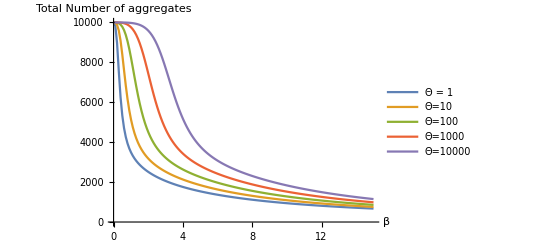

```mathematica
ListLinePlot[{(ⅇ^-J05+gamma×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J05×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))/(ⅇ^-J05+gamma×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J05×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))×10000,(ⅇ^-J1+gamma×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J1×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))/(ⅇ^-J1+gamma×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J1×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))×10000,(ⅇ^-J105+gamma×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J105×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))/(ⅇ^-J105+gamma×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J105×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))×10000,(ⅇ^-J2+gamma×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J2×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))/(ⅇ^-J2+gamma×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J2×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))×10000,
(ⅇ^-J205+gamma×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J205×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))/(ⅇ^-J205+gamma×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J205×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))×10000},DataRange->{0,15},PlotLegends->{"Θ = 1","Θ=10","Θ=100","Θ=1000","Θ=10000"},AxesLabel->{"β","Total Number of aggregates"}]
```

General::munfl: Exp[-717.887] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-731.693] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-745.498] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

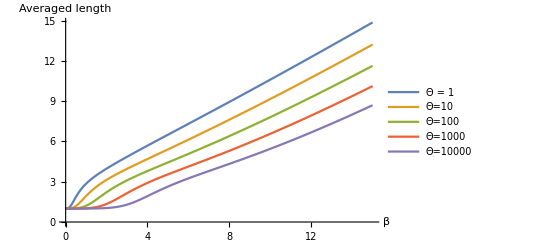

```mathematica
ListLinePlot[{(ⅇ^-J05+gamma×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J05×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))/(ⅇ^-J05+gamma×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J05×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)])),(ⅇ^-J1+gamma×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J1×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))/(ⅇ^-J1+gamma×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J1×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)])),(ⅇ^-J105+gamma×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J105×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))/(ⅇ^-J105+gamma×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J105×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)])),(ⅇ^-J2+gamma×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J2×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))/(ⅇ^-J2+gamma×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J2×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)])),
(ⅇ^-J205+gamma×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J205×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))/(ⅇ^-J205+gamma×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J205×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))},DataRange->{0,15},PlotLegends->{"Θ = 1","Θ=10","Θ=100","Θ=1000","Θ=10000"},AxesLabel->{"β","Averaged length"}]
```